```mathematica
Manipulate[

ArrayPlot[CellularAutomaton[{1018787,2,3},SeedRandom[seed];RandomChoice[{y*400,r*400,b*400}->{2,1,0}],400],250PlotRange->{{0,w},{0,w}},PlotLabel->Text[Style["initial density red "<>ToString[r],"Output",Bold]], ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},ImageSize->{500,300}],
{{seed,1234,"initial condition"},1000,1500,1},
{{r,0.333,"initial density red"},0.002,1},
{{y,0.333,"initial density yellow"},0.002,1},
{{b,0.333,"initial density blue"},0.002,1},Delimiter,
{{w,150,"zoom"},20,250,1}]
```

```mathematica
Manipulate[BlockRandom[626];
	ArrayPlot[
		CellularAutomaton[{1018787,3,3},RandomChoice[],60]
]
```

```mathematica
996772,895177,771502,942851,504876,930520,290177,178737,162904,733138,844381,1018787
```

```mathematica
Take[ResourceData["Three-Color Cellular Automaton Rules that are reversible"],20]
```

ResourceObject::notfname: The ResourceObject Three-Color Cellular Automaton Rules that are reversible could not be found.

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,20].

Take[$Failed,20]

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==0,r1+r3-b3,l1+l3-b1]+c>=2,1,0],2],3,4},SeedRandom[seed];Normal[SparseArray[Thread[RandomSample[Range[400],Round[d400]]->1],400]],250],ImageSize->{500,300},PlotRange->{{0,w},{0,w}},PlotLabel->Text[Style["initial density red "<>ToString[d],"Output",Bold]]],
{{seed,1234,"initial condition"},1000,1500,1},
{{d,0.5,"initial density red"},0.002,1},Delimiter,
{{w,150,"zoom"},20,250,1}]
```

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{294849496976490097794812493824,2},SeedRandom[seed];

Normal[Take[SparseArray[Thread[If[Round[d 300]==0,{},RandomSample[Range[300],Round[d 300]]]->3],400],s]],(Ceiling[2 s/3])],ImageSize->400,Frame->False],
{{seed,1234,"initial configuration"},1000,1500,1},
{{d,0.5,"initial black cell density"},0,1},Delimiter,
{{s,100,"zoom"},20,300,1}]
```

CellularAutomaton::rsize: The specified rule number 294849496976490097794812493824 is greater than the largest possible rule number (255).

ArrayPlot::mat: Argument CellularAutomaton[{294849496976490097794812493824,2},{0,0,3,3,3,0,0,3,3,0,«90»},67] at position 1 is not a list of lists.

CellularAutomaton::rsize: The specified rule number 294849496976490097794812493824 is greater than the largest possible rule number (255).

ArrayPlot::mat: Argument CellularAutomaton[{294849496976490097794812493824,2},{0,0,3,3,3,0,0,3,3,0,«90»},67] at position 1 is not a list of lists.

CellularAutomaton::rsize: The specified rule number 294849496976490097794812493824 is greater than the largest possible rule number (255).

ArrayPlot::mat: Argument CellularAutomaton[{294849496976490097794812493824,2},{0,0,3,3,3,0,0,3,3,0,«90»},67] at position 1 is not a list of lists.

```mathematica
CAruleAssociation[n_,a_]:=AssociationThread[Tuples[Range[a],3],IntegerDigits[n,a,a^3]]
CAcolorConvert[n_,a_,b_]:=With[{aRules=CAruleAssociation[n,a],bRules=CAruleAssociation[0,b]},FromDigits[Values@Part[Merge[{aRules,bRules},First],Key/@Keys[bRules]],b]]
```

```mathematica
CAcolorConvert[123,2,3]
```

972948365334

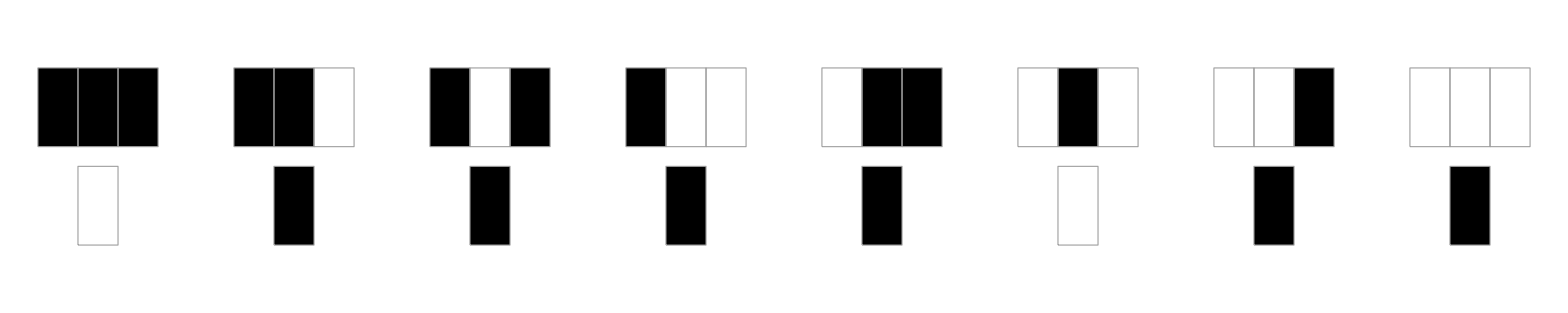

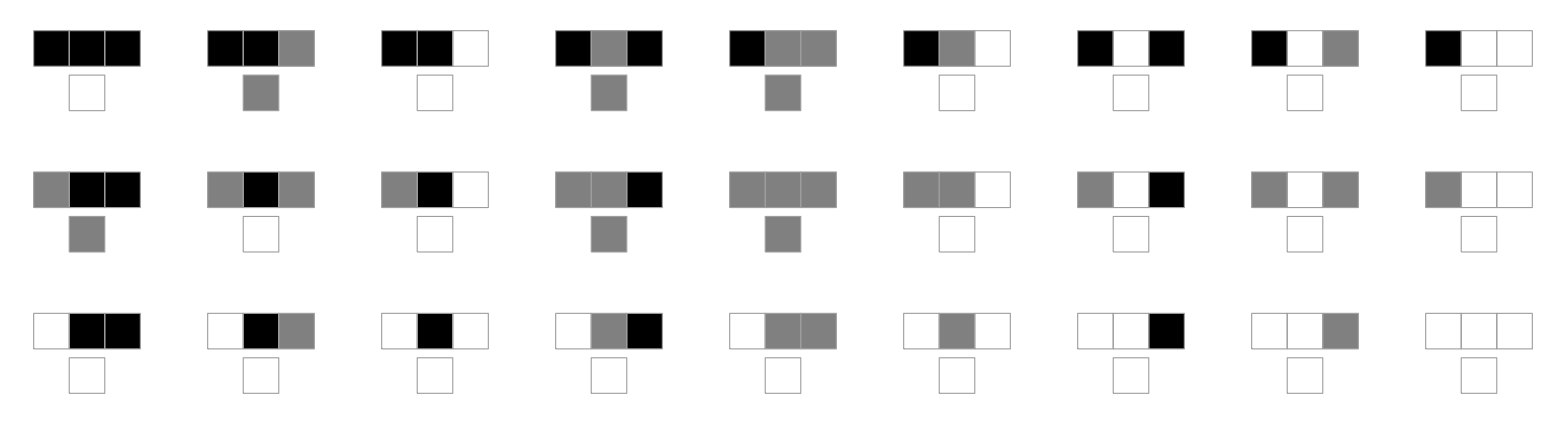

```mathematica
RulePlot@CellularAutomaton[{123,2}]
RulePlot@CellularAutomaton[{CAcolorConvert[123,2,3],3}]
```

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.1,.5,.4}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,3,3},{338557163619953682141694933300561896488,3,3},{313421633154342960352882914658469183496,3,3}}]
```

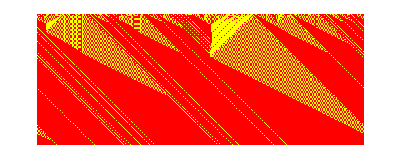

```mathematica
BlockRandom[SeedRandom[567]; 
 ArrayPlot[
  CellularAutomaton[{4196304428, 2, 2}, 
   RandomChoice[{.58, .42} -> {1, 0}, 500], 200], 
  ColorRules -> {0 -> Yellow, 
    1 ->  Red}, Frame -> False]]
```

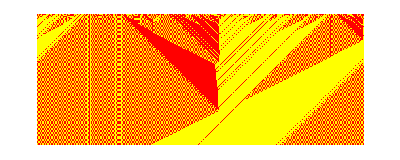

```mathematica
BlockRandom[SeedRandom[567]; 
 ArrayPlot[
  CellularAutomaton[{4196304428, 2,2}, 
   RandomChoice[{.48, .52} -> {1, 0}, 500], 200], 
  ColorRules -> {0 -> Yellow, 
    1 ->  Red}, Frame -> False]]
```

```mathematica
CAcolorConvert[4196304428,2,2]
```

44

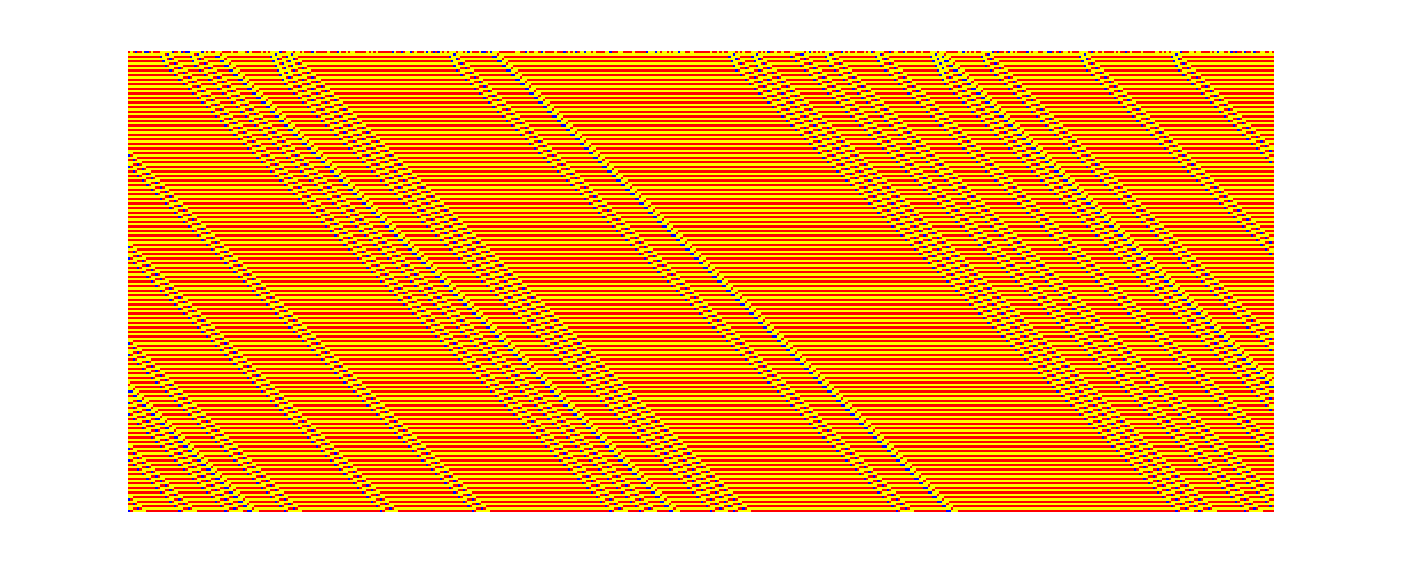

```mathematica
BlockRandom[SeedRandom[567]; 
 ArrayPlot[
  CellularAutomaton[{CAcolorConvert[98747747488,2,2], 3, 2}, 
   RandomChoice[{.1,.48, .42} -> {2,1, 0}, 500], 200], 
  ColorRules -> {0 -> Yellow, 
    1 ->  Red, 2-> Blue}, Frame -> False]]
```

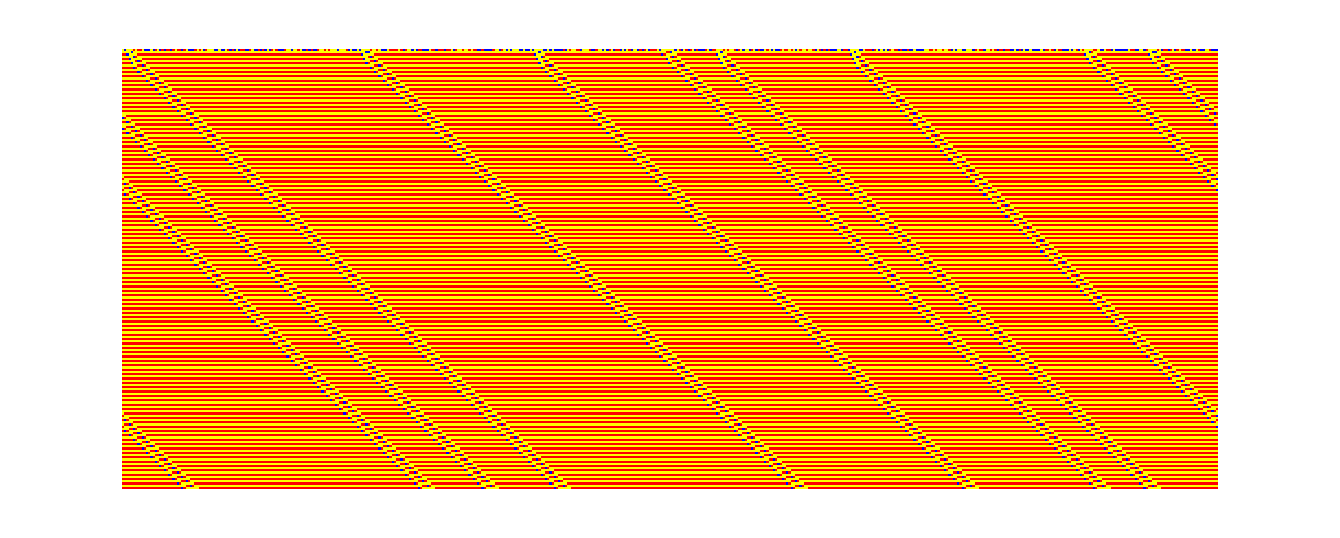

```mathematica
BlockRandom[SeedRandom[626]; 
 ArrayPlot[
  CellularAutomaton[{CAcolorConvert[98747747488,2,2], 3, 2}, 
   RandomChoice[{.33333,.33333, .33333} -> {2,1, 0}, 500], 200], 
  ColorRules -> {0 -> Yellow, 
    1 ->  Red, 2-> Blue}, Frame -> False]]
```

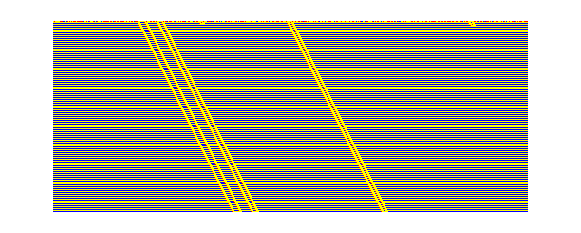

```mathematica
BlockRandom[SeedRandom[626]; 
 ArrayPlot[
  CellularAutomaton[{CAcolorConvert[4196304428,2,2], 3, 3}, 
   RandomChoice[{.1,.42, .48} -> {2,1, 0}, 500], 200], 
  ColorRules -> {0 -> Yellow, 
    1 ->  Red, 2-> Blue}, Frame -> False]]
```

```mathematica
ParallelTable[ BlockRandom[SeedRandom[828];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+b1+r3,l1+b3+l3]+c>=3,1,0],3],3,3},

RandomChoice[{.333,.333, .333}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,0,8,1}]
```

```mathematica
Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+b1+r3,l1+b3+l3]+c>=3,1,0]
```

{If[2+If[2==i,2+2+2,2+2+2]≥3,1,0],If[2+If[2==i,2+2+1,2+2+2]≥3,1,0],If[2+If[2==i,2+2+0,2+2+2]≥3,1,0],If[2+If[2==i,2+1+2,2+2+2]≥3,1,0],If[2+If[2==i,2+1+1,2+2+2]≥3,1,0],If[2+If[2==i,2+1+0,2+2+2]≥3,1,0],If[2+If[2==i,2+0+2,2+2+2]≥3,1,0],2173,If[If[0==i,0+2+0,0+0+0]≥3,1,0],If[If[0==i,0+1+2,0+0+0]≥3,1,0],If[If[0==i,0+1+1,0+0+0]≥3,1,0],If[If[0==i,0+1+0,0+0+0]≥3,1,0],If[If[0==i,0+0+2,0+0+0]≥3,1,0],If[If[0==i,0+0+1,0+0+0]≥3,1,0],If[If[0==i,0+0+0,0+0+0]≥3,1,0]}
 |  |  |  |

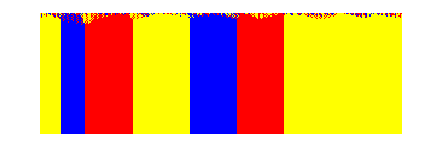
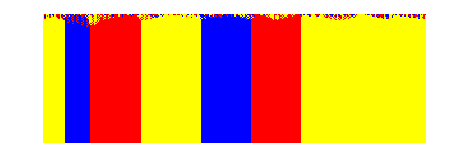

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/.neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,3],3,{{-7},{-4},{-1},{0},{1},{4},{7}}},

RandomChoice[{.333,.333, .333}->{2,1,0},300],100],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,3,4,1}]
```

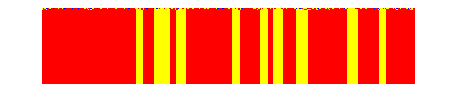
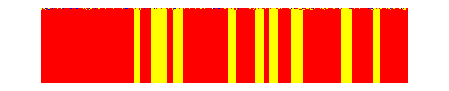

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/.neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,3],3,3},

RandomChoice[{.6,.1, .3}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,3,4,1}]
```

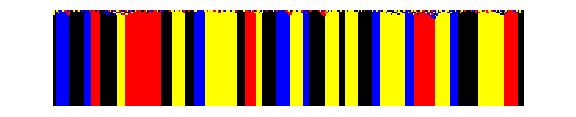

```mathematica
BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{3,2,1,0},7]/.neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,4],4,3},

RandomChoice[{.25,.25,.25,.25}->{3,2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red, 3-> Black},Frame->False, ImageSize->Large]]
```

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{3,2,1,0},7]/.neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,4],4,i},

RandomChoice[{.4,.2,.1,.3}->{3,2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red, 3-> Black},Frame->False]],{i,3,7,1}]
```

$Aborted

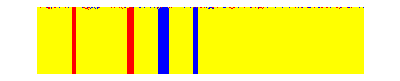
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[828];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/.neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:> First @ Commonest[neighbors]
 ,3],3,3},

RandomChoice[{.2,.2, .6}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,0,8,1}]
```

```mathematica
Tuples[{2,1,0},7]/.neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,1,2,1,1,1,2,1,1,2,2,2,2,1,1,2,1,0,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,1,0,2,2,2,2,1,0,2,0,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,1,0,2,2,2,2,1,0,2,0,0,2,2,2,2,2,2,2,2,0,2,2,2,2,1,0,2,0,0,2,2,0,2,0,0,0,0,0,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,1,2,1,1,1,2,1,1,2,2,2,2,1,1,2,1,0,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,1,0,2,2,2,2,1,0,2,0,0,2,2,2,2,1,2,2,2,2,2,1,2,1,1,1,2,1,1,2,2,2,2,1,1,2,1,0,2,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,2,2,2,1,1,2,1,0,2,1,1,1,1,1,1,1,1,2,1,0,1,1,1,0,1,0,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,1,0,2,2,2,2,1,0,2,0,0,2,2,2,2,1,1,2,1,0,2,1,1,1,1,1,1,1,1,2,1,0,1,1,1,0,1,0,2,2,2,2,1,0,2,0,0,2,1,0,1,1,1,0,1,0,2,0,0,0,1,0,0,0,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,1,0,2,2,2,2,1,0,2,0,0,2,2,2,2,2,2,2,2,0,2,2,2,2,1,0,2,0,0,2,2,0,2,0,0,0,0,0,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,1,0,2,2,2,2,1,0,2,0,0,2,2,2,2,1,1,2,1,0,2,1,1,1,1,1,1,1,0,2,1,0,1,1,0,0,0,0,2,2,2,2,1,0,2,0,0,2,1,0,1,1,0,0,0,0,2,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,0,2,2,2,2,1,0,2,0,0,2,2,0,2,0,0,0,0,0,2,2,2,2,1,0,2,0,0,2,1,0,1,1,0,0,0,0,2,0,0,0,0,0,0,0,0,2,2,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,1,2,2,2,2,2,1,2,2,2,2,2,2,2,2,1,1,2,1,2,2,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,0,2,2,2,2,1,2,2,2,2,2,1,2,1,1,1,2,1,0,2,2,2,2,1,0,2,0,0,2,2,2,2,1,1,2,1,2,2,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,0,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,0,1,1,1,1,1,1,1,1,1,2,1,0,1,1,1,0,1,0,2,2,2,2,1,2,2,2,2,2,1,2,1,1,1,2,1,0,2,2,2,2,1,0,2,0,0,2,1,2,1,1,1,2,1,0,1,1,1,1,1,1,1,1,1,2,1,0,1,1,1,0,1,0,2,2,2,2,1,0,2,0,0,2,1,0,1,1,1,0,1,0,2,0,0,0,1,0,0,0,0,2,2,2,2,1,1,2,1,2,2,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,0,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,0,1,1,1,1,1,1,1,1,1,2,1,0,1,1,1,0,1,0,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,2,1,2,1,1,1,2,1,0,1,1,1,1,1,1,1,1,1,2,1,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,2,1,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,0,0,1,0,1,1,0,0,0,0,2,2,2,2,1,2,2,2,0,2,1,2,1,1,1,2,1,0,2,2,0,2,1,0,0,0,0,2,1,2,1,1,1,2,1,0,1,1,1,1,1,1,1,1,1,2,1,0,1,1,1,0,1,0,2,2,0,2,1,0,0,0,0,2,1,0,1,1,1,0,1,0,0,0,0,0,1,0,0,0,0,2,1,2,1,1,1,2,1,0,1,1,1,1,1,1,1,1,1,2,1,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,2,1,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,0,0,1,0,1,1,0,0,0,0,2,2,0,2,1,0,0,0,0,2,1,0,1,1,1,0,1,0,0,0,0,0,1,0,0,0,0,2,1,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,2,2,2,2,2,0,2,0,0,2,2,2,2,2,2,2,2,0,2,2,2,2,1,1,2,1,0,2,2,0,2,1,0,0,0,0,2,2,2,2,2,0,2,0,0,2,2,0,2,1,0,0,0,0,2,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,0,2,2,2,2,1,1,2,1,0,2,2,0,2,1,0,0,0,0,2,2,2,2,1,1,2,1,0,2,1,1,1,1,1,1,1,0,2,1,0,1,1,0,0,0,0,2,2,0,2,1,0,0,0,0,2,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,0,2,0,0,2,2,0,2,1,0,0,0,0,2,0,0,0,0,0,0,0,0,2,2,0,2,1,0,0,0,0,2,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,1,2,2,2,0,2,1,2,1,1,1,2,1,0,2,2,0,2,1,0,0,0,0,2,1,2,1,1,1,2,1,0,1,1,1,1,1,1,1,1,0,2,1,0,1,1,0,0,0,0,2,2,0,2,1,0,0,0,0,2,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,2,1,1,1,2,1,0,1,1,1,1,1,1,1,1,0,2,1,0,1,1,0,0,0,0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,0,1,0,2,1,0,1,1,0,0,0,0,1,1,0,1,1,1,0,1,0,0,0,0,0,1,0,0,0,0,2,2,0,2,1,0,0,0,0,2,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0,1,1,0,0,0,0,1,1,0,1,1,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,0,2,0,0,2,2,0,2,1,0,0,0,0,2,0,0,0,0,0,0,0,0,2,2,0,2,1,0,0,0,0,2,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,2,1,0,0,0,0,2,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0,1,1,0,0,0,0,1,1,0,1,1,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

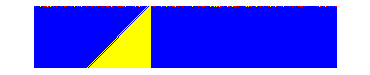
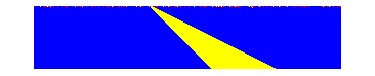
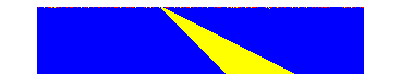
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+b1+r3,l1+b3+l3]+c>=3,1,0],3],3,3},

RandomChoice[{0.3,0.6,.1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,4}]
```

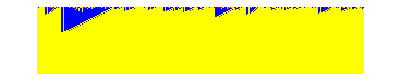
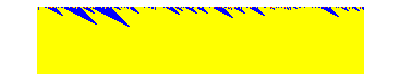
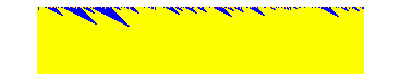
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+b1+r3,l1+b3+l3]+c>=3,1,0],3],3,3},

RandomChoice[{0.1,0.4,.5}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,4}]
```

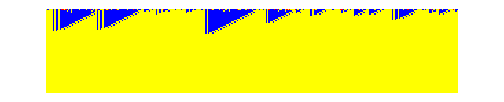
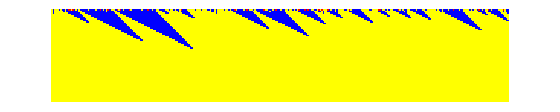
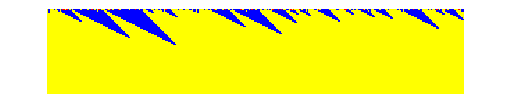
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+b1+r3,l1+b3+l3]+c>=3,1,0],3],3,3},

RandomChoice[{0.1,0.5,.4}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,4}]
```

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+b1+r3,l1+b3+l3]+c>=3,1,0],3],3,3},

RandomChoice[{1/3,1/3,1/3}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+b1+r3,l1+b3+l3]+c>=3,1,0],3],3,3},

RandomChoice[{0.1,0.7,.2}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+b1+r3,l1+b3+l3]+c>=3,1,0],3],3,3},

RandomChoice[{0.4,0.2,.4}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==0,r1+b1+r3,l1+b3+l3]+c>=3,1,0],3],3,k},

RandomChoice[{0.6,0.3,.1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{k,3,4}]
```

{-Graphics-,-Graphics-}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[828];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==i,r1+b1+r3,l1+b3+l3]+c>=3,1,0],3],3,3},

RandomChoice[{.6,.2, .2}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[626];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. {l3_,b3_,l1_,c_,r1_,b1_,r3_}:>If[If[c==3,r1+b1+r3,l1+b3+l3]+c>=3,1,0],2],3,k},

RandomChoice[{.4,.4,.2}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1-> Blue, 2 -> Red},Frame->False]],{i,4},{k,3,5}]
```